```mathematica
(*двумерный ряд распределения*)
```

```mathematica
p1=2(1/2)^6+2*3^2(1/2)^6
p2=(1/2)^6+3(1/2)^6+3(1/2)^6+9(1/2)^6+3(1/2)^6+3(1/2)^6
p3=3(1/2)^6+3(1/2)^6+(1/2)^6+9(1/2)^6+3(1/2)^6+3(1/2)^6
```

5/16

11/32

11/32

```mathematica
p4=(4!)/(2!2!)(1/2)^6+4*2(1/2)^6+(1/2)^6
p5=(1/2)^6+2(1/2)^6+(1/2)^6+4(1/2)^6+4(1/2)^6+4*2(1/2)^6+2(4!)/(2!2!)(1/2)^6+(4!)/(2!2!)(1/2)^6+4(1/2)^6
p6=4(1/2)^6+(1/2)^6+2(1/2)^6
```

15/64

21/32

7/64

```mathematica
p4+p5+p6
```

1

```mathematica
p7=6(1/2)^6
p8=2(1/2)^6+15(1/2)^6+(4*5!)/(3!2!)(1/2)^6
p9=(1/2)^6
```

3/32

57/64

1/64

```mathematica
p7+p8+p9
```

1

```mathematica
p10=(1/2)^6
p11=(1/2)^6+6(1/2)^6+(6!)/(4!2!)(1/2)^6+(6!)/(3!3!)(1/2)^6+(6!)/(4!2!)(1/2)^6+6(1/2)^6
```

1/64

63/64

```mathematica
p10+p11
```

1

```mathematica
Ver00=p1^4
```

625/65536

```mathematica
Ver01=p2*p4^3+p1*p2*p4^2+p1^2*p2*p4+p1^3p2
```

240625/8388608

```mathematica
Ver11=p2*p6*p1^2+p2*p4*p6*p1+p2*p4^2p6+p1^2*p2*p6+p1*p2*p6*p4+p1^2*p2*p6+3p3 p6 p1^2+2p3 p4 p6 p1+p3 p4^2p6
```

155925/4194304

```mathematica
Ver22=p2 p5 p9 p6+p2^2p6^2+p2^2p6 p6+p3 p6 p2 p6+p3 p5 p9 p6+p3^2p6^2
```

13475/2097152

```mathematica
Ver40=p2*p5*p8*p11
```

829521/4194304

```mathematica
Ver13=0+p2*p5^2*p9+p2^2p6 p5+p3 p6 p2 p5
```

40425/2097152

```mathematica
Ver30=p2 p5 p8 p10+ p2 p5 p7 p8+p2 p4 p5 p8+p1 p2 p5 p8
```

276507/2097152

```mathematica
Ver20=p2 p5 p7^2+p1 p2 p5 p7+p1^2p2 p5+p2 p4^2p5+p1 p2 p4 p5+p2 p4 p5 p7
```

270501/4194304

```mathematica
Ver12=p2 p5 p7 p9+p1 p2 p5 p9+p1 p3 p6 p2+p2 p4 p5 p9+p1 p2^2 p6+p2 p4 p6 p2+p2 p5 p9 p4+p3 p6 p2 p4+p3 p4 p6 p2+p2^2p6 p4+p3 p6 p1 p2+p2^2p6 p1
```

32879/1048576

```mathematica
(Ver00+Ver01+Ver20+Ver30+Ver40)+(Ver01+Ver11+Ver12+Ver13)+(Ver20+Ver12+Ver22)+(Ver30+Ver13)+Ver40
```

1

```mathematica
(*линия регрессии*)
```

```mathematica
Ver00
```

625/65536

```mathematica
Ver11
```

155925/4194304

```mathematica
Ver22
```

13475/2097152

```mathematica
Ver01
```

240625/8388608

```mathematica
Ver20
```

270501/4194304

```mathematica
Ver30
```

276507/2097152

```mathematica
Ver40
```

829521/4194304

```mathematica
Ver12
```

32879/1048576

```mathematica
Ver13
```

40425/2097152

```mathematica
ξ=RandomChoice[{Ver00,Ver11,Ver22,Ver01,Ver20,Ver30,Ver40,Ver12,Ver13,Ver01,Ver20,Ver30,Ver40,Ver12,Ver13}->{{0,0},{1,1},{2,2},{0,1},{0,2},{0,3},{0,4},{1,2},{1,3},{1,0},{2,0},{3,0},{4,0},{2,1},{3,1}},100]
```

{{1,2},{4,0},{1,1},{0,4},{0,4},{0,3},{1,1},{3,1},{4,0},{3,0},{0,4},{3,0},{4,0},{4,0},{0,4},{0,4},{0,4},{2,0},{1,0},{0,4},{4,0},{4,0},{4,0},{4,0},{2,0},{0,3},{0,4},{0,3},{4,0},{0,3},{4,0},{0,4},{0,4},{0,4},{3,0},{0,4},{4,0},{1,0},{0,4},{1,0},{0,2},{3,0},{0,4},{1,0},{0,3},{2,0},{0,4},{0,4},{0,4},{3,0},{4,0},{3,0},{0,4},{2,0},{4,0},{3,0},{3,0},{4,0},{4,0},{0,3},{3,1},{4,0},{2,0},{0,3},{4,0},{0,3},{0,2},{4,0},{1,1},{0,4},{0,0},{3,0},{4,0},{0,4},{4,0},{0,4},{0,3},{0,2},{2,1},{4,0},{0,4},{2,1},{0,2},{4,0},{0,1},{2,1},{2,0},{1,2},{0,3},{0,4},{4,0},{1,0},{4,0},{1,0},{0,4},{0,4},{2,0},{0,4},{2,0},{0,4}}

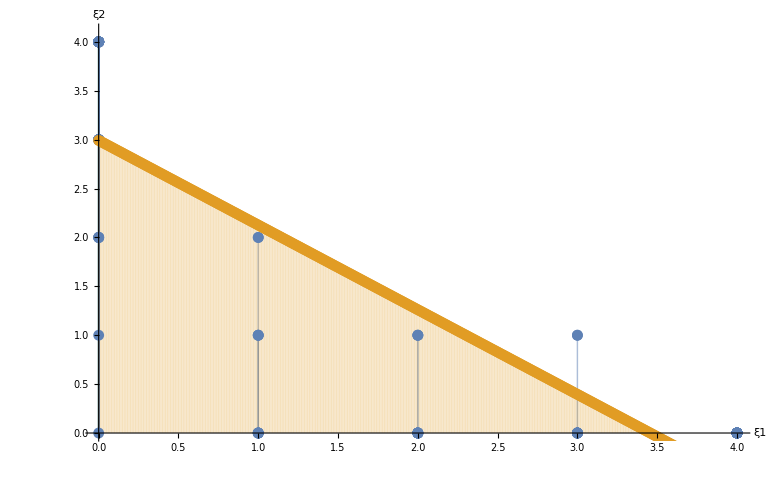

```mathematica
line=Normal[LinearModelFit[ξ,x,x]];
m=Table[{x,line},{x,0,4,0.01}];

ListPlot[{ξ,m},PlotRange->{0,4.1},Filling->Axis,AxesLabel->{"ξ1","ξ2"},PlotStyle->PointSize[0.01]]
```

```mathematica
N[2Ver40+2Ver30+2Ver20+Ver11+2Ver12+Ver01]
```

0.916801

```mathematica
ξ09={{4,0},{0,4},{3,0},{0,3},{2,0},{0,2},{1,1},{1,2},{2,1},{0,1}};
```

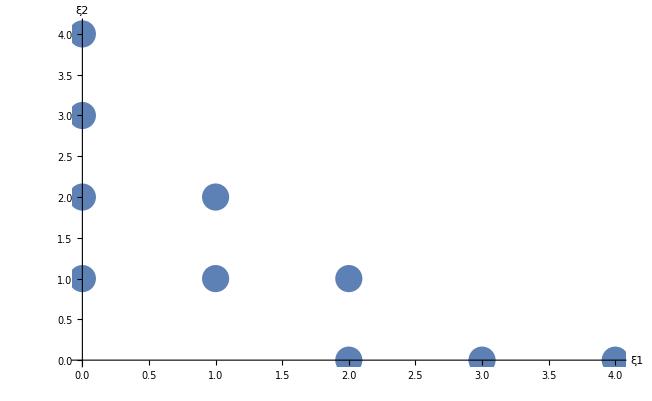

```mathematica
ListPlot[ξ09,PlotRange->{0,4.1},AxesLabel->{"ξ1","ξ2"},PlotStyle->PointSize[0.03]]
```

```mathematica
0.4323+0.1978+0.1511+0.1165
```

0.8977

```mathematica
ξ109={{0,0},{1,1},{2,2},{3,3},{4,4}};
```

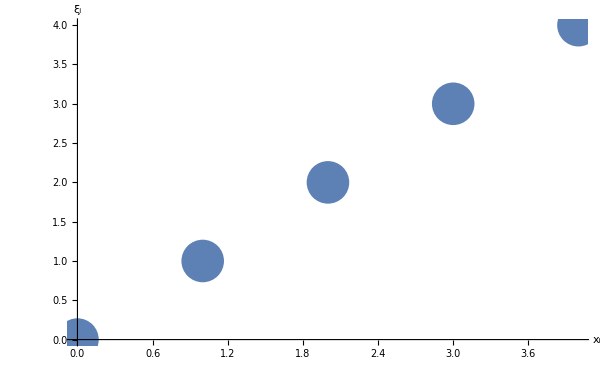

```mathematica
ListPlot[ξ109,AxesLabel->{"x_i","ξ_i"},PlotStyle->PointSize[0.05]]
```